```mathematica
{t,t}+({Cos[t],Sin[t]}-{t,t})/2
```

{t+1/2 (-t+Cos[t]),t+1/2 (-t+Sin[t])}

```mathematica
-f[x]Log[f[x]]
```

-f[x] Log[f[x]]

```mathematica
With[{f=Function[x, x x]},-f[x]Log[f[x]]]
```

-x^2 Log[x^2]

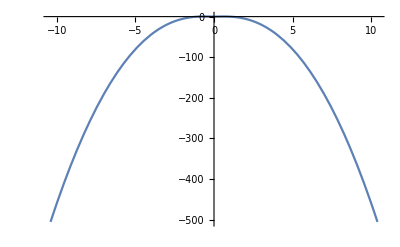

```mathematica
Plot[-x^2 Log[x^2],{x,-10.392304845413262,10.392304845413262}]
```

```mathematica
With[{f=SInc},-f[x]Log[f[x]]]
```

-Log[SInc[x]] SInc[x]

```mathematica
With[{f=Sinc},-f[x]Log[f[x]]]
```

-Log[Sinc[x]] Sinc[x]

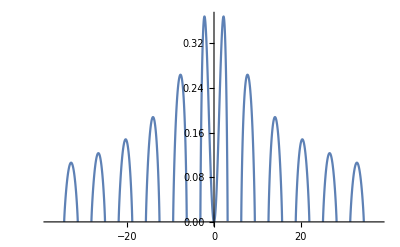

```mathematica
Plot[-Log[Sinc[x]] Sinc[x],{x,-37.69911184307752,37.69911184307752}]
```

```mathematica
∑_(i=0)^n f[i]
```

∑_(i=0)^n f[i]

```mathematica
∑_(i=0)^n f[x]
```

(1+n) f[x]

```mathematica
∑_(i=0)^n f[x]/g[x]
```

((1+n) f[x])/g[x]

```mathematica
D[x Exp[x],x]
```

ⅇ^x+ⅇ^x x

```mathematica
D[x Exp[x],{x,5}]
```

5 ⅇ^x+ⅇ^x x

```mathematica
∑_(i=0)^n f[i]/g[i]
```

∑_(i=0)^n f[i]/g[i]

```mathematica
∑_(i=0)^(n-1) f[i]/g[i]
```

∑_(i=0)^(-1+n) f[i]/g[i]

```mathematica
Dt[f[x],{x,5}]
```

f^(5)[x]

```mathematica
Apply[f,List[x]]
```

f[x]

```mathematica
Dt[f[t]g[t]]
```

Dt[t] g[t] f'[t]+Dt[t] f[t] g'[t]

```mathematica
{t,t}.RotationMatrix[t]
```

{t Cos[t]+t Sin[t],t Cos[t]-t Sin[t]}

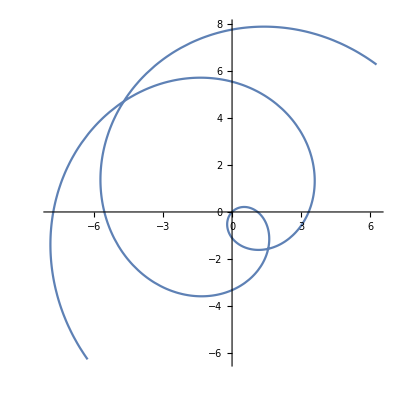

```mathematica
ParametricPlot[
{t Cos[t]+t Sin[t],t Cos[t]-t Sin[t]}
,{t,-2π,2π}]
```

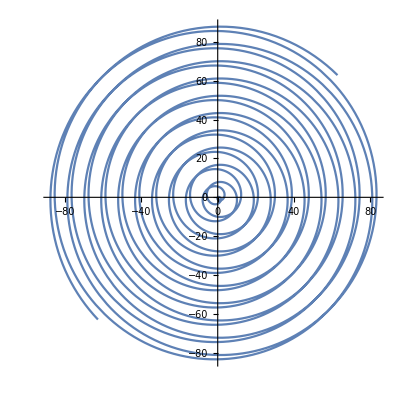

```mathematica
ParametricPlot[
{t Cos[t]+t Sin[t],t Cos[t]-t Sin[t]}
,{t,-20π,20π}]
```

```mathematica
{t,t}.RotationMatrix[π t]
```

{t Cos[π t]+t Sin[π t],t Cos[π t]-t Sin[π t]}

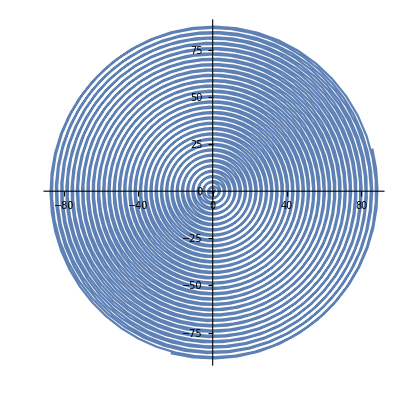

```mathematica
ParametricPlot[
{t Cos[π t]+t Sin[π t],t Cos[π t]-t Sin[π t]}
,{t,-20π,20π}]
```

```mathematica
{t,t}.RotationMatrix[t Exp[-t^2/2]]
```

{t Cos[ⅇ^(-t^2/2) t]+t Sin[ⅇ^(-t^2/2) t],t Cos[ⅇ^(-t^2/2) t]-t Sin[ⅇ^(-t^2/2) t]}

General::munfl: Exp[-1973.92] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1973.76] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

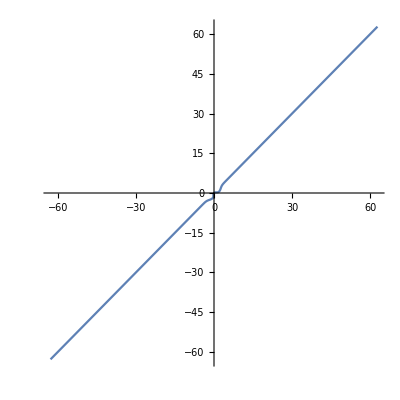

```mathematica
ParametricPlot[
{t Cos[ⅇ^(-t^2/2) t]+t Sin[ⅇ^(-t^2/2) t],t Cos[ⅇ^(-t^2/2) t]-t Sin[ⅇ^(-t^2/2) t]}
,{t,-20π,20π}]
```

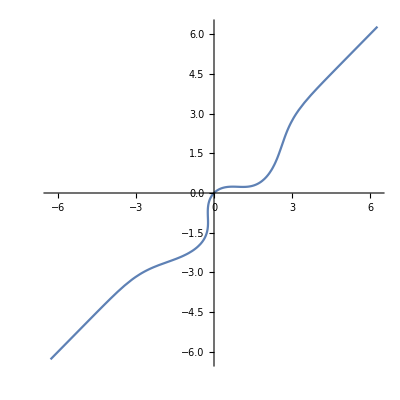

```mathematica
ParametricPlot[
{t Cos[ⅇ^(-t^2/2) t]+t Sin[ⅇ^(-t^2/2) t],t Cos[ⅇ^(-t^2/2) t]-t Sin[ⅇ^(-t^2/2) t]}
,{t,-2π,2π}]
```

```mathematica
{t,t}.RotationMatrix[Exp[-t^2/2]]
```

{t Cos[ⅇ^(-t^2/2)]+t Sin[ⅇ^(-t^2/2)],t Cos[ⅇ^(-t^2/2)]-t Sin[ⅇ^(-t^2/2)]}

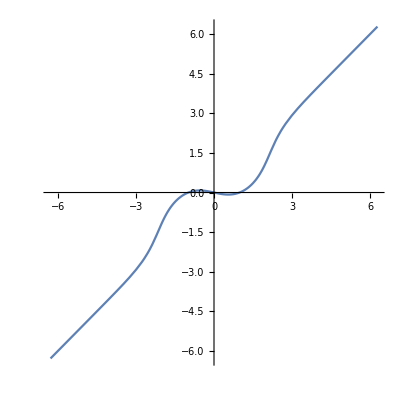

```mathematica
ParametricPlot[
{t Cos[ⅇ^(-t^2/2)]+t Sin[ⅇ^(-t^2/2)],t Cos[ⅇ^(-t^2/2)]-t Sin[ⅇ^(-t^2/2)]}
,{t,-2π,2π}]
```

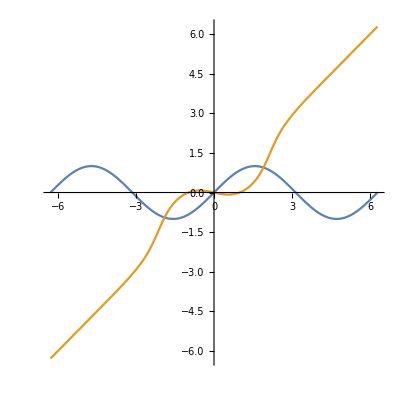

```mathematica
ParametricPlot[{
{t,Sin[t]},
{t Cos[ⅇ^(-t^2/2)]+t Sin[ⅇ^(-t^2/2)],t Cos[ⅇ^(-t^2/2)]-t Sin[ⅇ^(-t^2/2)]}
},{t,-2π,2π}]
```

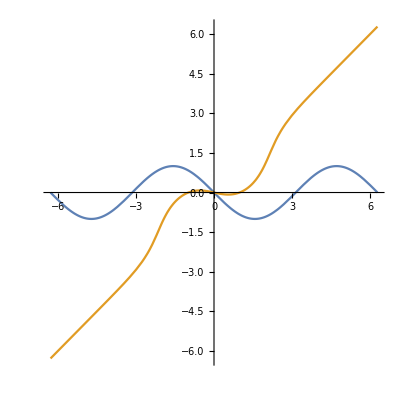

```mathematica
ParametricPlot[{
{t,-Sin[t]},
{t Cos[ⅇ^(-t^2/2)]+t Sin[ⅇ^(-t^2/2)],t Cos[ⅇ^(-t^2/2)]-t Sin[ⅇ^(-t^2/2)]}
},{t,-2π,2π}]
```

```mathematica
{t,-Sin[t]}.RotationMatrix[2π-π/4]
```

{t/(√2)+Sin[t]/(√2),t/(√2)-Sin[t]/(√2)}

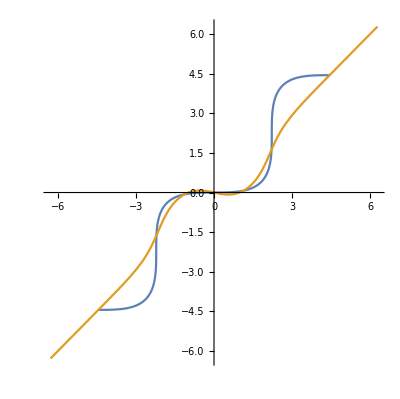

```mathematica
ParametricPlot[{
{t/(√2)+Sin[t]/(√2),t/(√2)-Sin[t]/(√2)},
{t Cos[ⅇ^(-t^2/2)]+t Sin[ⅇ^(-t^2/2)],t Cos[ⅇ^(-t^2/2)]-t Sin[ⅇ^(-t^2/2)]}
},{t,-2π,2π}]
```

```mathematica
Multicolumn[Region/@{Tetrahedron[],Cube[],Octahedron[],Dodecahedron[],Icosahedron[]},Sequence[5,Spacings->1]]
```

-Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-

```mathematica
Volume[Tetrahedron[]]
```

1/(6 √2)

```mathematica
Graphics3D[Tetrahedron[]]
```

-Graphics3D-

```mathematica
Laplacian[f[x,y],{x,y}]
```

f^(0,2)[x,y]+f^(2,0)[x,y]

```mathematica
Laplacian[f[x],{x}]
```

f''[x]

```mathematica
SphericalPlot3D[1,{θ,0,2π}]
```

SphericalPlot3D::argrx: SphericalPlot3D called with 2 arguments; 3 arguments are expected.

SphericalPlot3D[1,{θ,0,2 π}]

```mathematica
SphericalPlot3D[1,{θ,0,2π},{ϕ,0,2π}]
```

-Graphics3D-

```mathematica
SphericalPlot3D[θ/ϕ,{θ,0,2π},{ϕ,0,2π}]
```

-Graphics3D-

```mathematica
SphericalPlot3D[Sinc@θ,{θ,0,2π},{ϕ,0,2π}]
```

-Graphics3D-

```mathematica
SphericalPlot3D[Sinc@θ+Sinc@ϕ,{θ,0,2π},{ϕ,0,2π}]
```

-Graphics3D-

```mathematica
SphericalPlot3D[θ ϕ,{θ,0,2π},{ϕ,0,2π}]
```

-Graphics3D-

```mathematica
SphericalPlot3D[θ ϕ,{θ,0,π},{ϕ,0,π}]
```

-Graphics3D-

```mathematica
FullSimplify[Normalize@D[{x,x^2},x].Normalize@D[{x,x},x],x∈Reals]
```

(1+2 x)/(√(2+8 x^2))

```mathematica
Limit[NIntegrate[(1+2 x)/(√(2+8 x^2)),{x,-a,a}],a->Infinity]
```

NIntegrate::nlim: x = -1. a is not a valid limit of integration.

lim_(a→∞) NIntegrate[(1+2 x)/(√(2+8 x^2)),{x,-a,a}]

```mathematica
Manipulate[
NIntegrate[(1+2 x)/(√(2+8 x^2)),{x,-a,a}]
,{a,0,10000}]
```

```mathematica
Manipulate[
NIntegrate[((1+2 x)/(√(2+8 x^2)))/(2a),{x,-a,a}]
,{a,0,10000}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.310833}. NIntegrate obtained 0.000379826 and 0.0000436778 for the integral and error estimates.

```mathematica
Limit[NIntegrate[((1+2 x)/(√(2+8 x^2)))/(2a),{x,-a,a}],a->∞]
```

NIntegrate::nlim: x = -1. a is not a valid limit of integration.

lim_(a→∞) NIntegrate[(1+2 x)/(√(2+8 x^2) (2 a)),{x,-a,a}]

```mathematica
MemoryInUse[]
```

225664640

```mathematica
MemoryInUse[]
```

227640008

```mathematica
Apply[MemoryInUse,{}]
```

227692016

```mathematica
PDF[NormalDistribution[],x]
```

(ⅇ^(-x^2/2))/(√(2 π))

```mathematica
ⅇ^(-x^2/2)
```

ⅇ^(-x^2/2)

```mathematica
{x,x}.RotationMatrix[ⅇ^(-x^2/2)]
```

{x Cos[ⅇ^(-x^2/2)]+x Sin[ⅇ^(-x^2/2)],x Cos[ⅇ^(-x^2/2)]-x Sin[ⅇ^(-x^2/2)]}

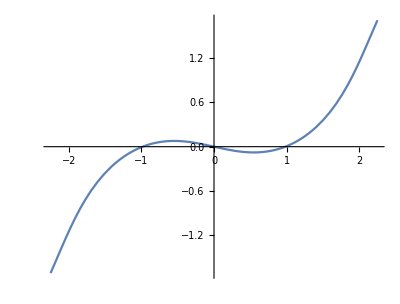

```mathematica
ParametricPlot[
{x Cos[ⅇ^(-x^2/2)]+x Sin[ⅇ^(-x^2/2)],x Cos[ⅇ^(-x^2/2)]-x Sin[ⅇ^(-x^2/2)]}
,{x,-2,2}]
```

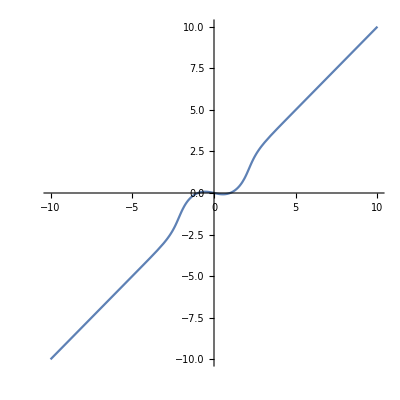

```mathematica
ParametricPlot[
{x Cos[ⅇ^(-x^2/2)]+x Sin[ⅇ^(-x^2/2)],x Cos[ⅇ^(-x^2/2)]-x Sin[ⅇ^(-x^2/2)]}
,{x,-10,10}]
```

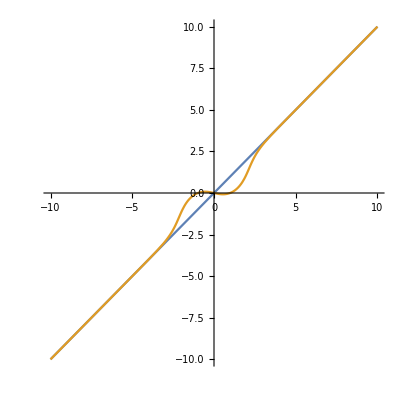

```mathematica
ParametricPlot[{
{x,x},
{x Cos[ⅇ^(-x^2/2)]+x Sin[ⅇ^(-x^2/2)],x Cos[ⅇ^(-x^2/2)]-x Sin[ⅇ^(-x^2/2)]}
},{x,-10,10}]
```

```mathematica
{x,x}.(a RotationMatrix[ⅇ^(-x^2/2)])
```

{a x Cos[ⅇ^(-x^2/2)]+a x Sin[ⅇ^(-x^2/2)],a x Cos[ⅇ^(-x^2/2)]-a x Sin[ⅇ^(-x^2/2)]}

```mathematica
Manipulate[
ParametricPlot[{
{x,x},
{x Cos[ⅇ^(-x^2/2)]+x Sin[ⅇ^(-x^2/2)],x Cos[ⅇ^(-x^2/2)]-x Sin[ⅇ^(-x^2/2)]},
{a x Cos[ⅇ^(-x^2/2)]+a x Sin[ⅇ^(-x^2/2)],a x Cos[ⅇ^(-x^2/2)]-a x Sin[ⅇ^(-x^2/2)]}
},{x,-10,10}]
,{a,0,1}]
```

```mathematica
(1-a){x,x}+a {x Cos[ⅇ^(-x^2/2)]+x Sin[ⅇ^(-x^2/2)],x Cos[ⅇ^(-x^2/2)]-x Sin[ⅇ^(-x^2/2)]}
```

{(1-a) x+a (x Cos[ⅇ^(-x^2/2)]+x Sin[ⅇ^(-x^2/2)]),(1-a) x+a (x Cos[ⅇ^(-x^2/2)]-x Sin[ⅇ^(-x^2/2)])}

```mathematica
(1-b){x,x}+b {x Cos[ⅇ^(-x^2/2)]+x Sin[ⅇ^(-x^2/2)],x Cos[ⅇ^(-x^2/2)]-x Sin[ⅇ^(-x^2/2)]}
```

{(1-b) x+b (x Cos[ⅇ^(-x^2/2)]+x Sin[ⅇ^(-x^2/2)]),(1-b) x+b (x Cos[ⅇ^(-x^2/2)]-x Sin[ⅇ^(-x^2/2)])}

```mathematica
Manipulate[
ParametricPlot[{
{x,x},
{x Cos[ⅇ^(-x^2/2)]+x Sin[ⅇ^(-x^2/2)],x Cos[ⅇ^(-x^2/2)]-x Sin[ⅇ^(-x^2/2)]},
{a x Cos[ⅇ^(-x^2/2)]+a x Sin[ⅇ^(-x^2/2)],a x Cos[ⅇ^(-x^2/2)]-a x Sin[ⅇ^(-x^2/2)]},
{(1-b) x+b (x Cos[ⅇ^(-x^2/2)]+x Sin[ⅇ^(-x^2/2)]),(1-b) x+b (x Cos[ⅇ^(-x^2/2)]-x Sin[ⅇ^(-x^2/2)])}
},{x,-10,10}]
,{a,0,1},{b,0,1}]
```

```mathematica
Manipulate[
ParametricPlot[{
{x,x},
{x Cos[ⅇ^(-x^2/2)]+x Sin[ⅇ^(-x^2/2)],x Cos[ⅇ^(-x^2/2)]-x Sin[ⅇ^(-x^2/2)]},
{a x Cos[ⅇ^(-x^2/2)]+a x Sin[ⅇ^(-x^2/2)],a x Cos[ⅇ^(-x^2/2)]-a x Sin[ⅇ^(-x^2/2)]},
{(1-b) x+b (x Cos[ⅇ^(-x^2/2)]+x Sin[ⅇ^(-x^2/2)]),(1-b) x+b (x Cos[ⅇ^(-x^2/2)]-x Sin[ⅇ^(-x^2/2)])}
},{x,-10,10}]
,{a,0,100},{b,0,100}]
```

```mathematica
8-5x+4 x x x - x x x x
```

8-5 x+4 x^3-x^4

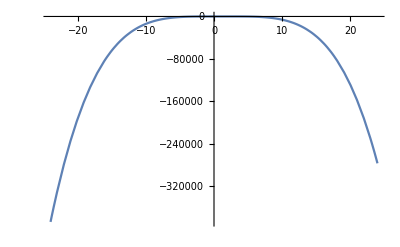

```mathematica
Plot[8-5 x+4 x^3-x^4,{x,-24.,24.}]
```

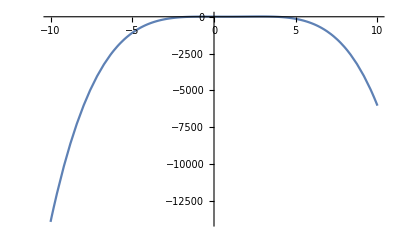

```mathematica
Plot[8-5 x+4 x^3-x^4,{x,-10,10}]
```

```mathematica
8-5 x+4 x^3-x^4/.x->x+y
```

8-5 (x+y)+4 (x+y)^3-(x+y)^4

```mathematica
Expand[8-5 (x+y)+4 (x+y)^3-(x+y)^4]
```

8-5 x+4 x^3-x^4-5 y+12 x^2 y-4 x^3 y+12 x y^2-6 x^2 y^2+4 y^3-4 x y^3-y^4

```mathematica
Plot3D[8-5 x+4 x^3-x^4-5 y+12 x^2 y-4 x^3 y+12 x y^2-6 x^2 y^2+4 y^3-4 x y^3-y^4,{x,-0.13667203293192237,0.13667203293192237},{y,-0.13667203293192237,0.13667203293192237}]
```

-Graphics3D-

```mathematica
Plot3D[8-5 x+4 x^3-x^4-5 y+12 x^2 y-4 x^3 y+12 x y^2-6 x^2 y^2+4 y^3-4 x y^3-y^4,{x,-10,10},{y,-10,10}]
```

-Graphics3D-

```mathematica
f=InverseFunction[g]
```

g^(-1)

```mathematica
f
```

g^(-1)

```mathematica
g[x+f[x]]
```

g[x+g^(-1)[x]]

```mathematica
ClearAll[f]
```

```mathematica
f[x]+InverseFunction[f][x]==x
```

f[x]+f^(-1)[x]==x

```mathematica
Solve[f[x]+(f^(-1))[x]==x,f]
```

{}

```mathematica
Integrate[g'[x]f[x],x]
```

∫f[x] g'[x]ⅆx

```mathematica
Integrate[g'[x]f[x],x]+f'[x]g[x]==a +f'[x]g[x]
```

∫f[x] g'[x]ⅆx+g[x] f'[x]==a+g[x] f'[x]

```mathematica
f[x]g'[x]+f'[x]g[x]==a+f'[x]g[x]
```

g[x] f'[x]+f[x] g'[x]==a+g[x] f'[x]

```mathematica
f[x]g[x]-f'[x]g[x]==a
```

f[x] g[x]-g[x] f'[x]==a

```mathematica
Dt[x^2+y^2==1]
```

2 x Dt[x]+2 y Dt[y]==0

```mathematica
Solve[2 x Dt[x]+2 y Dt[y]==0, Dt[x]]
```

{{Dt[x]→-(y Dt[y])/x}}

```mathematica
Plot3D[(x^2+y^2)^2,{x,y}∈Disk[{0,0},3]]
```

-Graphics3D-

```mathematica
Plot3D[(x^2+y^2)^2,{x,y}∈Disk[{0,0},5]]
```

-Graphics3D-

```mathematica
Plot3D[{(x^2+y^2)^2,2(x^2-y^2)},{x,y}∈Disk[{0,0},5]]
```

-Graphics3D-

```mathematica
RegionPlot[(x^2+y^2)^2==2(x^2-y^2),{x,y}∈Disk[{0,0},5]]
```

-Graphics-

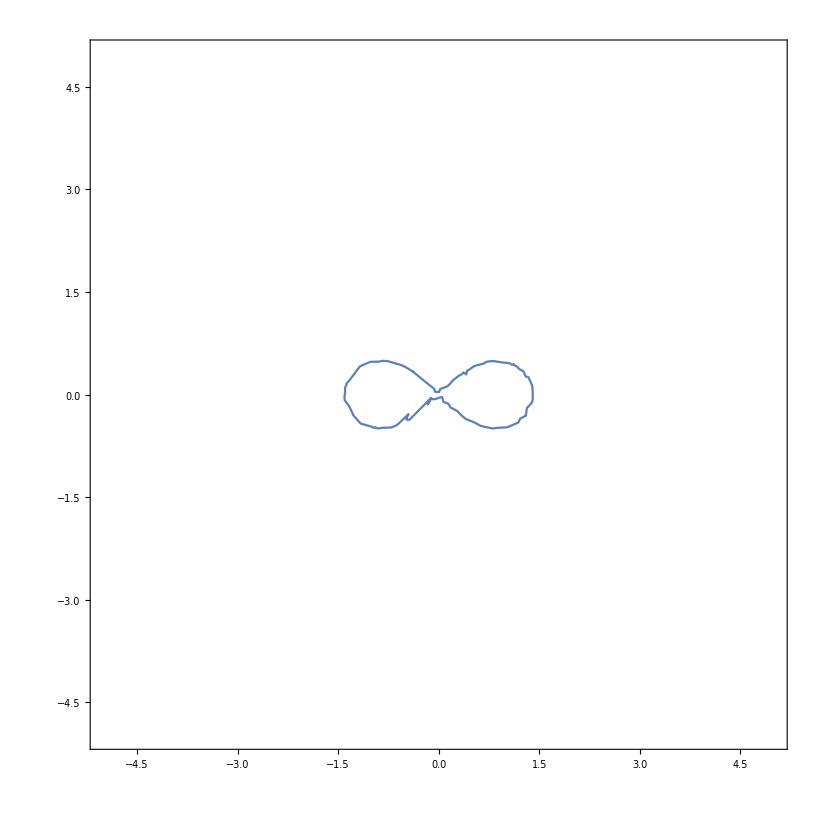

```mathematica
ContourPlot[(x^2+y^2)^2==2(x^2-y^2),{x,y}∈Disk[{0,0},5]]
```